```mathematica
month=3;
day=31;
```

```mathematica
cToF[q_]:=UnitConvert[q,"DegreesFahrenheit"]
```

```mathematica
weatherYear[year_]:=cToF/@WeatherData["Los Angeles", "MeanTemperature",{{year, month, day}, {year+1, month, day}, "Day"}]["Values"]
```

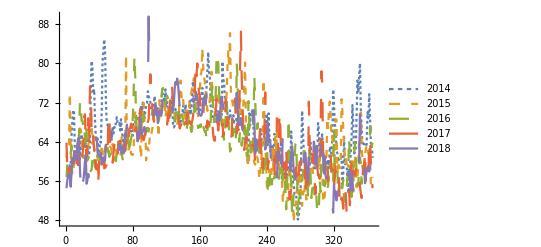

```mathematica
ListLinePlot[Table[weatherYear[y],{y,2014,2018}],PlotLegends->Table[y,{y,2014,2018}],PlotStyle->{Dashing[Tiny],Dashing[Small],Dashing[Medium],Dashing[Large],AbsoluteDashing[10000]}]
```

```mathematica
Predict
```

```mathematica
a+b
```

a+b

```mathematica
(a^2-b^2)/(a-b)
```

```mathematica
Simplify[(a^2-b^2)/(a-b)]
```

a+b